## PAH

### function

```mathematica
benzenegraph[cen_,side_]:={{EdgeForm[{Black}],GrayLevel[(1-0)],Polygon[{{cen⟦1⟧,cen⟦2⟧+side/(√3)},{cen⟦1⟧+side/2,cen⟦2⟧+side/(2 √3)},{cen⟦1⟧+side/2,cen⟦2⟧-side/(2 √3)},{cen⟦1⟧,cen⟦2⟧-side/(√3)},{cen⟦1⟧-side/2,cen⟦2⟧-side/(2 √3)},{cen⟦1⟧-side/2,cen⟦2⟧+side/(2 √3)}}]} };
pahgraph[cen_,side_,zigzag_,armchair_]:=Graphics[ Table[benzenegraph[{cen⟦1⟧+j*side+Mod[i,2]*side/2,cen⟦2⟧-i*(√3)/2*side},side],{i,0,armchair-1},{j,0,zigzag-1}] ];
pahgraphMultiRow[cen_,side_,zigzag_,armchair_]:=Graphics[{Table[benzenegraph[{cen⟦1⟧+k*side,cen⟦2⟧},side],{k,0,zigzag-1}], Table[benzenegraph[{cen⟦1⟧-IntegerPart[(2*zigzag-1-j)/(zigzag+0.2)]*side/2+Mod[j+1,zigzag]*side,cen⟦2⟧-(2*i+1)*(√3)/2*side-IntegerPart[(j+1)/(zigzag-0.2)]*(√3)/2*side},side],{i,0,(armchair-3)/2},{j,0,zigzag*2-2}] }]
```

```mathematica
benzenegraphRot[cen_,side_]:={{EdgeForm[{Black}],GrayLevel[(1-0)],Polygon[{{cen⟦2⟧+side/(√3),cen⟦1⟧},{cen⟦2⟧+side/(2 √3),cen⟦1⟧+side/2},{cen⟦2⟧-side/(2 √3),cen⟦1⟧+side/2},{cen⟦2⟧-side/(√3),cen⟦1⟧},{cen⟦2⟧-side/(2 √3),cen⟦1⟧-side/2},{cen⟦2⟧+side/(2 √3),cen⟦1⟧-side/2}}]} };
pahgraphRot[cen_,side_,zigzag_,armchair_]:=Graphics[ Table[benzenegraphRot[{cen⟦1⟧+j*side+Mod[i,2]*side/2,cen⟦2⟧-i*(√3)/2*side},side],{i,0,armchair-1},{j,0,zigzag-1}] ];
```

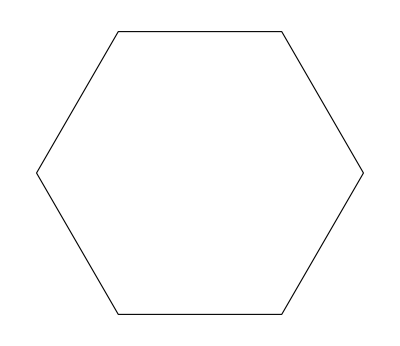

```mathematica
Graphics[benzenegraphRot[{0,0},1]]
```

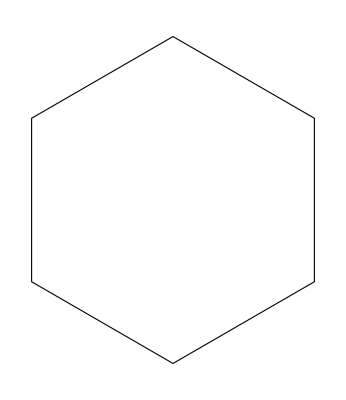

```mathematica
Graphics[benzenegraph[{0,0},1]]
```

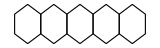

```mathematica
R51fig=Show[{	pahgraph[{0,0},1,5,1]	}]
```

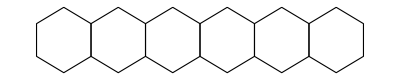

```mathematica
R61fig=Show[{pahgraph[{0,0},1,6,1]}]
```

```mathematica
R61figrot=Rotate[Show[{pahgraph[{0,0},1,6,1]}],90Degree]
```

-Graphics-

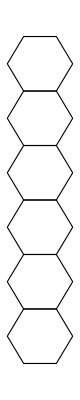

```mathematica
R61figrot2=Show[{pahgraphRot[{0,0},1,6,1]}]
```

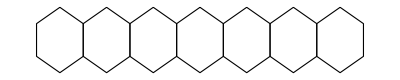

```mathematica
R71fig=Show[{	pahgraph[{0,0},1,7,1]	}]
```

```mathematica
R71figrot=Rotate[Show[{	pahgraph[{0,0},1,7,1]	}],90 Degree]
```

-Graphics-

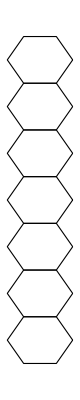

```mathematica
R71figrot2=Show[{	pahgraphRot[{0,0},1,7,1]	}]
```

```mathematica
R33fig=Show[{	pahgraphMultiRow[{0,0},1,3,3]	}]
```

-Graphics-

## PES

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\dodo\Desktop\soothair_g09\paper\2_Tri-Sin\jpcl

```mathematica
y0deltaE={{0.419,16.4},{0.559,9.5},{0.696,4.4},{0.51,10.6}} (*R51,R61,R71,R33 b3lyp/6-311+g(d,p) R11-83.5*)
```

{{0.419,16.4},{0.559,9.5},{0.696,4.4},{0.51,10.6}}

```mathematica
fitline=Fit[y0deltaE,{1,x},x]
```

33.1155-41.924 x

```mathematica
logf[x_]:=N[Log[3*Exp[-x/(1500/491)]]]
```

```mathematica
f[x_]:=N[3*Exp[-x/(1500/491)]]
```

```mathematica
f[4]
```

f[4]

```mathematica
inversef[f_]:=N[-Log[f/3]*1500/491]
```

```mathematica
inversef[1]
```

3.35625

```mathematica
rightticks[min_,max_]:=Table[If[EvenQ[i],{i,f[i]},{i,f[i]}],{i,Ceiling[min],Floor[max],1}]
```

```mathematica
rightticks[4,16]
```

{{4,f[4]},{5,f[5]},{6,f[6]},{7,f[7]},{8,f[8]},{9,f[9]},{10,f[10]},{11,f[11]},{12,f[12]},{13,f[13]},{14,f[14]},{15,f[15]},{16,f[16]}}

```mathematica
rightticks={(*{inversef[1],1},*){inversef[0.8],0.8,{0.005,0}},{inversef[0.7],,{0.005,0}},{inversef[0.6],,{0.005,0}},{inversef[0.5],0.5,{0.005,0}},{inversef[0.4],,{0.005,0}},{inversef[0.3],,{0.005,0}},{inversef[0.2],0.2,{0.005,0}},{inversef[0.1],0.1,{0.015,0}},{inversef[0.09],,{0.005,0}},{inversef[0.08],,{0.005,0}},{inversef[0.07],,{0.005,0}},{inversef[0.06],,{0.005,0}},{inversef[0.05],0.05,{0.005,0}},{inversef[0.04],,{0.005,0}},{inversef[0.03],,{0.005,0}},{inversef[0.02],0.02,{0.005,0}}}
```

{{4.03795,0.8,{0.005,0}},{4.44589,Null,{0.005,0}},{4.91682,Null,{0.005,0}},{5.47381,0.5,{0.005,0}},{6.15551,Null,{0.005,0}},{7.03437,Null,{0.005,0}},{8.27307,0.2,{0.005,0}},{10.3906,0.1,{0.015,0}},{10.7125,Null,{0.005,0}},{11.0723,Null,{0.005,0}},{11.4803,Null,{0.005,0}},{11.9512,Null,{0.005,0}},{12.5082,0.05,{0.005,0}},{13.1899,Null,{0.005,0}},{14.0687,Null,{0.005,0}},{15.3074,0.02,{0.005,0}}}

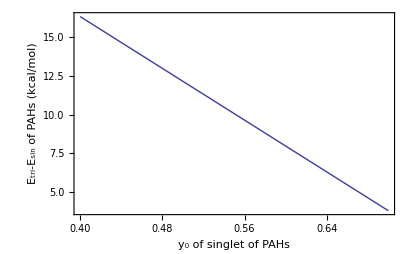

```mathematica
plotframe={{Style["E_tri-E_sin of PAHs (kcal/mol)",Italic,17],Style["Mole Fraction Ratio of Triplet and Singlet",Italic,17]},{Style["y_0 of singlet of PAHs",Italic,17],}};
lineplot=Plot[fitline,{x,0.4,0.7},Frame-> {{True,True},{True,True}},FrameLabel->plotframe,PlotRange-> {Automatic,Automatic},
                  AspectRatio-> 1/GoldenRatio,FrameTicks-> {{Automatic,rightticks},{Automatic, Automatic}},
                  AxesStyle->White,FrameStyle-> 15]
```

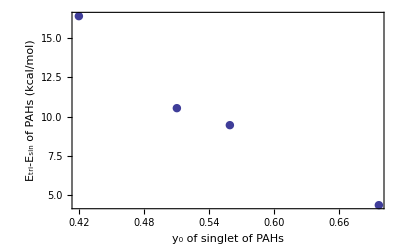

```mathematica
plotframe={{Style["E_tri-E_sin of PAHs (kcal/mol)",Italic,17],Style["Mole Fraction Ratio of Triplet and Singlet",Italic,17]},{Style["y_0 of singlet of PAHs",Italic,17],}};
datapoints=ListPlot[y0deltaE,
Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
FrameTicks-> {{Automatic,Automatic},{Automatic, None}},
                  AspectRatio-> 1/GoldenRatio,
                  AxesStyle->White,
                  PlotMarkers-> {Automatic,Medium},
                 FrameStyle-> 15
                    (*PlotLabel->Style["R1→ P1, Θ = 1 atm","Title",Bold,15]*)]
```

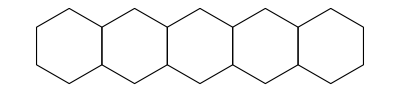
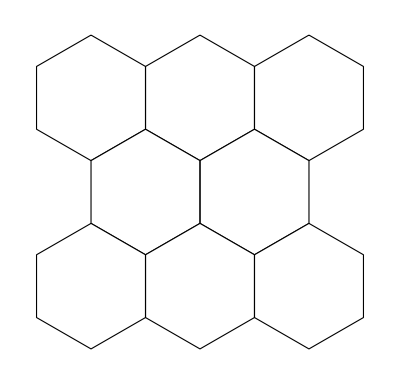
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Filenames={R51fig,R61figrot2,R71figrot2,R33fig}
```

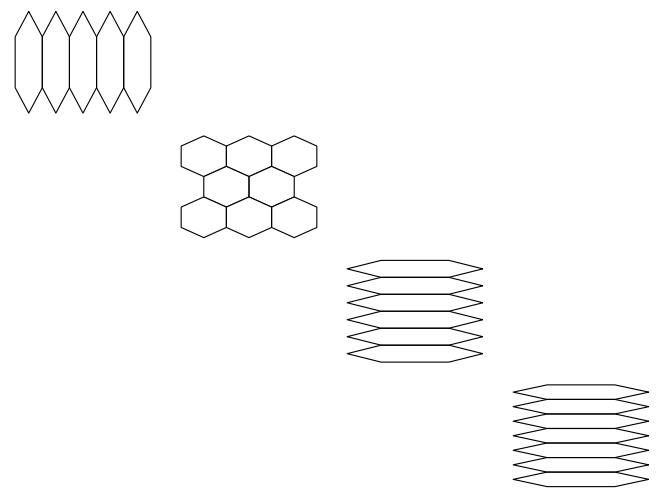

```mathematica
(*imagesize={0.075,0.025,0.025,0.050};*)
imagesize={0.075,0.02,0.02,0.050};
formular="ΔE = -42.0 y_0 + 33.2";
pah=Graphics[
{Table[Inset[Filenames⟦i⟧,y0deltaE⟦i⟧,Automatic,imagesize⟦i⟧],{i,1,4}],
Text[Style[formular,{20,Italic}],{0.47,5}]},
Frame-> {{True,True},{True,True}},FrameLabel->plotframe,
FrameTicks-> {{Automatic,Automatic},{Automatic, None}},
                  AspectRatio-> 1/GoldenRatio,
                 FrameStyle-> 15
]
```

```mathematica
Show[lineplot,datapoints ,pah(*,
        Graphics[{{Text[Style["PENTACENE",17],{0.419,16.3},{-1.2,0}]},{Text[Style["HEXACENE",17],{0.559,9.5},{-1.2,-1}]},{Text[Style["HEPTACENE",17],{0.696,4.4},{1,-2}]}}]*)]
```